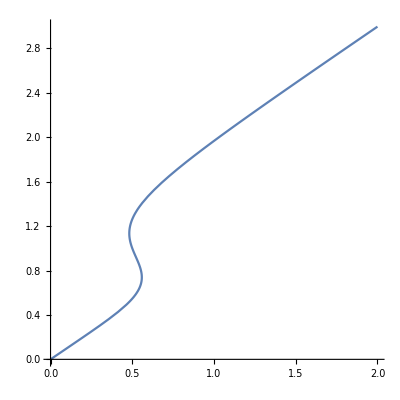

```mathematica
n = 5;
f = 1;
smin = 0;
smax = 2;
xdot = s - x + f*x^n/(1+x^n);
sol = NSolve[xdot==0, s];
tempSol = Solve[2 == s/.sol, x];
ParametricPlot[{ s/.sol[[1]], x}, {x,0,Evaluate[x/.Last[tempSol]]}, AspectRatio->1]
```

0.5

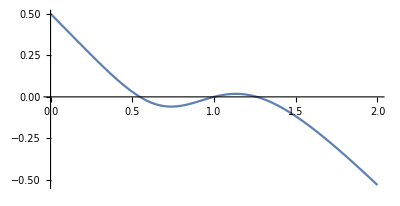

```mathematica
s = 0.5
ParametricPlot[{x, xdot}, {x,0,2}]
```